NDSolveValue::berr: The scaled boundary value residual error of 4.42753 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolveValue::berr: The scaled boundary value residual error of 1.00538 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolveValue::berr: The scaled boundary value residual error of 82.0692 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

General::stop: Further output of NDSolveValue::berr will be suppressed during this calculation.

3.78811

{-3.97944,-2.72789,-2.90315,-2.84925,-2.86483,-2.86023,-2.86158,-2.86118,-2.8613,-2.86126}

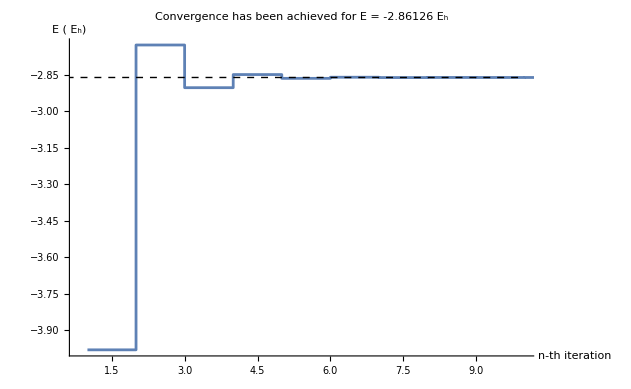

```mathematica
prevE=1.;
currE=0.;
prec=10^-4;

rho=0;
rMin=$MachineEpsilon;
rMax=50.;

n=1;
l=0;

vNuc=-2/r;

{t,vals}=Reap[While[Abs[prevE-currE]>prec,
prevE=currE;
uHart=NDSolveValue[{uH''[r]==-rho/r,uH[rMin]==0,uH[rMax]==1},uH,{r,rMin,rMax},Method->"Adams"];
alpha=(2-uHart[rMax])/rMax;
vHart=uHart[r]/r+alpha;
vHart/=2.;
(*vX=((-3 rho)/(4 Pi^2 r^2))^(1/3);
rs=(3r^2/rho)^(1/3);
ec=a Log[rs]+b-a/3+c*2/3 rs Log[rs]+(2d-c)rs/3;
vE=Piecewise[{{a,rs<=1}}];*)
vX=0.;
vE=0.;
Vtot=vNuc+vHart+(vX+vE)/2.;
{gden,gdefun}=NDEigensystem[{-1/2psi''[r]+(Vtot+(l(l+1))/(2r^2))psi[r],DirichletCondition[psi[r]==0,True]},psi,{r,rMin,rMax},All,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.15}}}]//Transpose//Sort//First;
gdNorm=NIntegrate[gdefun[r],{r,rMin,rMax},AccuracyGoal->4];
gdefunN=gdefun[r]/Sqrt[1];
rho=2 gdefunN^2;
Ehart=NIntegrate[vHart rho,{r,rMin,rMax},Method->"GlobalAdaptive",AccuracyGoal->4]/2.;
currE=2 gden-Ehart;
Sow[currE]
]]//Last//First//AbsoluteTiming;
t
vals
ListStepPlot[vals,PlotRange->All,PlotLabel->StringForm["Convergence has been achieved for E = ``  E_h",Last[vals]],Epilog->{Dashed,Line[{{0,Last[vals]},{Length@vals,Last[vals]}}]} ,AxesLabel->{"n-th iteration","E ( E_h)"}]
```

```mathematica
i=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics/Report for the exam/DFTHe.jl/calcRes.tsv","Table"]//Flatten
```

{-3.95629,-2.59599,-2.99734,-2.82621,-2.8993,-2.86775,-2.88133,-2.87548,-2.878,-2.87691,-2.87738,-2.87718,-2.87727,-2.87723,-2.87724,-2.87724,-2.87724,-2.87724,-2.87724}

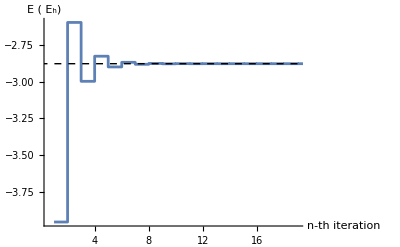

```mathematica
l=ListStepPlot[i,PlotRange->All,Epilog->{Dashed,Line[{{0,Last[i]},{Length@i,Last[i]}}]} ,AxesLabel->{"n-th iteration","E ( E_h)"}]
```

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics/Report for the exam/DFTHe.jl/calcRes.pdf",l]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics/Report for the exam/DFTHe.jl/calcRes.pdf

```mathematica
i2=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics/Report for the exam/DFTHe.jl/n_convRes.tsv","Table"]//Flatten
```

{-2.86974,-2.87576,-2.87686,-2.87724,-2.87741,-2.87751,-2.87756,-2.8776,-2.87762,-2.87764,-2.87765,-2.87766,-2.87767,-2.87767,-2.87768,-2.87768,-2.87768,-2.87769,-2.87769,-2.87769,-2.87769,-2.87769,-2.87769,-2.87769,-2.87769,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777,-2.8777}

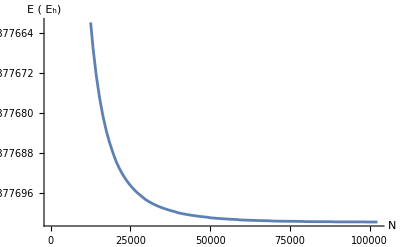

```mathematica
d=ListLinePlot[Transpose[{1024Range[1,100],i2}],PlotRange->Automatic,AxesLabel->{"N","E ( E_h)"}]
```

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics/Report for the exam/DFTHe.jl/n_convRes.pdf",d]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics/Report for the exam/DFTHe.jl/n_convRes.pdf